# Simulate distribution of mode and quantile in marginalized distribution to check BAT MCMC implementation.

```mathematica
nBins=100; Clear[f];
f[x_]:=400-x^2 (* the sample function *)
xMin=-20;
xMax= 20;
dX=(xMax-xMin)/nBins;
nExperiments=100;
nSamples=10^5;
DistributeDefinitions[nBins,nExperiments,nSamples];
binHighEdges=Table[i*dX,{i,nBins}]
SeedRandom[21062010]
```

{2/5,4/5,6/5,8/5,2,12/5,14/5,16/5,18/5,4,22/5,24/5,26/5,28/5,6,32/5,34/5,36/5,38/5,8,42/5,44/5,46/5,48/5,10,52/5,54/5,56/5,58/5,12,62/5,64/5,66/5,68/5,14,72/5,74/5,76/5,78/5,16,82/5,84/5,86/5,88/5,18,92/5,94/5,96/5,98/5,20,102/5,104/5,106/5,108/5,22,112/5,114/5,116/5,118/5,24,122/5,124/5,126/5,128/5,26,132/5,134/5,136/5,138/5,28,142/5,144/5,146/5,148/5,30,152/5,154/5,156/5,158/5,32,162/5,164/5,166/5,168/5,34,172/5,174/5,176/5,178/5,36,182/5,184/5,186/5,188/5,38,192/5,194/5,196/5,198/5,40}

## Calculate the probability histogram for single event to be in bin j

```mathematica
histo=Table[Integrate[f[x],{x,xMin+i*dX,xMin+(i+1)*dX}],{i,0,nBins-1}]
```

{1192/375,3544/375,5848/375,8104/375,10312/375,12472/375,14584/375,16648/375,18664/375,20632/375,22552/375,24424/375,26248/375,28024/375,29752/375,31432/375,33064/375,34648/375,36184/375,37672/375,39112/375,40504/375,41848/375,43144/375,44392/375,45592/375,46744/375,47848/375,48904/375,49912/375,50872/375,51784/375,52648/375,53464/375,54232/375,54952/375,55624/375,56248/375,56824/375,57352/375,57832/375,58264/375,58648/375,58984/375,59272/375,59512/375,59704/375,59848/375,59944/375,59992/375,59992/375,59944/375,59848/375,59704/375,59512/375,59272/375,58984/375,58648/375,58264/375,57832/375,57352/375,56824/375,56248/375,55624/375,54952/375,54232/375,53464/375,52648/375,51784/375,50872/375,49912/375,48904/375,47848/375,46744/375,45592/375,44392/375,43144/375,41848/375,40504/375,39112/375,37672/375,36184/375,34648/375,33064/375,31432/375,29752/375,28024/375,26248/375,24424/375,22552/375,20632/375,18664/375,16648/375,14584/375,12472/375,10312/375,8104/375,5848/375,3544/375,1192/375}

100

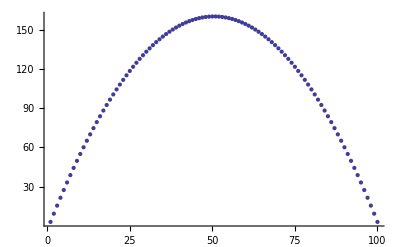

```mathematica
Length[histo]
ListPlot[histo//N]
```

normalize to 1

```mathematica
histo = histo/Total[histo//N];
Total[histo]
```

1.

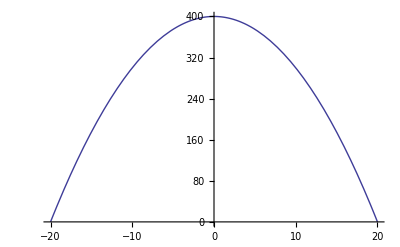

```mathematica
Plot[f[x],{x,xMin,xMax}]
```

## The cumulative

```mathematica
cdf=Accumulate[histo]
DistributeDefinitions[cdf]
```

{0.000298,0.001184,0.002646,0.004672,0.00725,0.010368,0.014014,0.018176,0.022842,0.028,0.033638,0.039744,0.046306,0.053312,0.06075,0.068608,0.076874,0.085536,0.094582,0.104,0.113778,0.123904,0.134366,0.145152,0.15625,0.167648,0.179334,0.191296,0.203522,0.216,0.228718,0.241664,0.254826,0.268192,0.28175,0.295488,0.309394,0.323456,0.337662,0.352,0.366458,0.381024,0.395686,0.410432,0.42525,0.440128,0.455054,0.470016,0.485002,0.5,0.514998,0.529984,0.544946,0.559872,0.57475,0.589568,0.604314,0.618976,0.633542,0.648,0.662338,0.676544,0.690606,0.704512,0.71825,0.731808,0.745174,0.758336,0.771282,0.784,0.796478,0.808704,0.820666,0.832352,0.84375,0.854848,0.865634,0.876096,0.886222,0.896,0.905418,0.914464,0.923126,0.931392,0.93925,0.946688,0.953694,0.960256,0.966362,0.972,0.977158,0.981824,0.985986,0.989632,0.99275,0.995328,0.997354,0.998816,0.999702,1.}

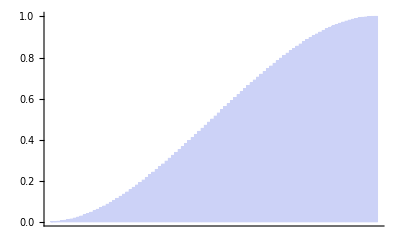

```mathematica
BarChart[cdf]
```

## Inverse - transform using binary search

```mathematica
locatr[array_, target_]:=Module[{high,low,probe,n},
n=Length[array];
high=n+1;
low=0;
(* check for boundaries *)
If[target<0 || target > 1,
Return[0]
];
While[high-low>1,
probe=Floor[(low+high)/2];
If[array[[probe]]<target,
low=probe;,
high=probe;
];
];
Return[high];
]
DistributeDefinitions[locatr];
temp={0.39348720457881686,0.6321492583604866,0.7769051112890548,0.8647039742630842,0.9179566765447413,0.9502560731911153,0.9698466475473605,0.9817289315358033,0.9889359010822064,0.9933071490757152,0.9959584450049855,0.9975665372740593,0.9985418945388994,0.9991334786241984,0.9994922925097304,0.9997099241324361,0.9998419243841301,0.9999219865838723,0.9999705467627,1.0000000000000002};
locatr[temp,0.2]==1
locatr[temp,0.4]==2
locatr[temp,0.80]==4
locatr[temp,1.4]==0
locatr[temp,-0.4]==0
```

True

True

True

«2 more identical outputs»

## Find mode, quantiles for ONE experiment

```mathematica
FindModeQuantilesSingleExp[]:=Module[{retValues,uniforms,EPDF,ECDF,parallel,temp},
(* use paralel version *)
parallel=False;
retValues={};
(* the uniform RV as input *)
uniforms=Table[Random[],{nSamples}];
If[parallel,
DistributeDefinitions[uniforms];
(* generate the events in bins directly *)
temp=ParallelMap[locatr[cdf,#] &,uniforms,Method->"CoarsestGrained"];
EPDF=BinCounts[temp ,{1,nBins}];
,
(*temp=Map[locatr[cdf,#] &,uniforms];*)
EPDF=BinCounts[ Map[locatr[cdf,#] &,uniforms],{1,nBins}];
];

(* various quantiles *)
ECDF=Accumulate[EPDF]/Total[EPDF];
AppendTo[retValues,locatr[ECDF,0.05] ];
AppendTo[retValues,locatr[ECDF,0.10] ];
AppendTo[retValues,locatr[ECDF,0.16] ];
AppendTo[retValues,locatr[ECDF,0.84] ];
AppendTo[retValues,locatr[ECDF,0.90] ];
AppendTo[retValues,locatr[ECDF,0.95] ];

(* bins with mode *)
AppendTo[retValues,Flatten[Position[EPDF, Max[EPDF]]] ];

Return[retValues];
]
DistributeDefinitions[FindModeQuantilesSingleExp];
AbsoluteTiming[FindModeQuantilesSingleExp[] ]
```

{5.607035,{14,20,26,75,81,87,{46}}}

## Generate many experiments. Maybe faster if paralleldo?

```mathematica
Clear[FindModeQuantilesManyExp]
FindModeQuantilesManyExp[]:=Module[{histos,temp,nQuantities,parallel},
parallel=True;
(* create histogram for each quantity of interest *)
temp=FindModeQuantilesSingleExp[];
nQuantities=Length[temp];
DistributeDefinitions[nQuantities];
histos = Table[0,{i,1,nQuantities},{k,1,nBins}];
(* slows down extremely, why? *)
If[parallel,
SetSharedVariable[histos];
(* loop over all experiments *)
ParallelDo[
(* generate new experiment *)
temp=FindModeQuantilesSingleExp[];
(* add one in the bin that was found as 16%, mode ... *)
Do[++histos[[j,temp[[j]] ]],{j,nQuantities}];
,{k,nExperiments},
Method-> "CoarsestGrained" 
];
];

If[!parallel,
Do[
(* generate new experiment *)
temp=FindModeQuantilesSingleExp[];
(* add one in the bin that was found as 16%, mode ... *)
Do[++histos[[j,temp[[j]] ]],{j,nQuantities}];
,{k,nExperiments}
];
];
Return[histos];
]

temp=AbsoluteTiming[FindModeQuantilesManyExp[] ];
Print["Time = "<>ToString[temp[[1]] ] ]
histos=temp[[2]];
```

Time = 581.460037

Compare speedup from parallelization

```mathematica
AbsoluteTiming[Table[FindModeQuantilesSingleExp[],{10}]]
AbsoluteTiming[ParallelTable[FindModeQuantilesSingleExp[],{10},Method-> "CoarsestGrained" ]]
```

{56.077941,{{14,20,26,75,81,87,{55}},{14,20,26,75,81,87,{52}},{14,20,26,75,81,87,{49}},{14,20,26,75,81,87,{52}},{14,20,26,75,81,87,{51}},{14,20,26,75,81,87,{56}},{14,20,26,75,81,87,{51}},{14,20,26,75,81,87,{56}},{14,20,26,75,81,87,{52,54}},{14,20,26,75,81,87,{52}}}}

{55.611402,{{14,20,26,75,81,87,{52}},{14,20,26,75,81,87,{58}},{14,20,26,75,81,87,{49,53}},{14,20,26,75,81,87,{50}},{14,20,26,75,81,87,{45}},{14,20,26,75,81,87,{48}},{14,20,26,75,81,87,{48}},{14,20,26,75,81,87,{51}},{14,20,26,75,81,87,{56}},{14,20,26,75,81,87,{57}}}}

## plot distributions

explicit data for plot testing

```mathematica
(*histos={{196,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{196,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{196,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,196,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,196,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,117,80,0,0,0,0,0,0,0,0,0,0,0,0,0},{196,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};*)
quantiles={"5%","10%","16%","84%","90%","95%"};
quantiles={5,10,16,84,90,95};
Map[ToString[#]<>"%"&,quantiles]
```

{5%,10%,16%,84%,90%,95%}

distr. of mode

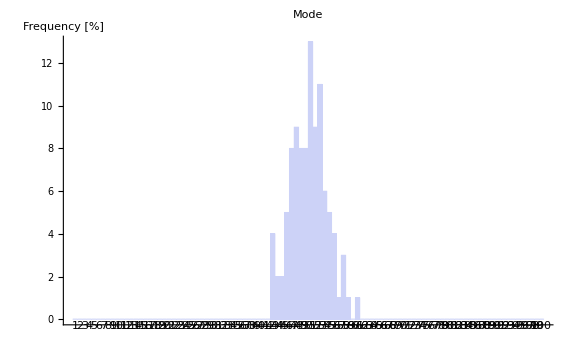

```mathematica
BarChart[histos[[-1]]/Total[histos[[-1]] ]*100,PlotLabel->"Mode",AxesLabel-> "Frequency [%]" ,ChartLabels->Table[ToString[i],{i,nBins}],ImageSize-> Large]
```

distr. of the quantiles

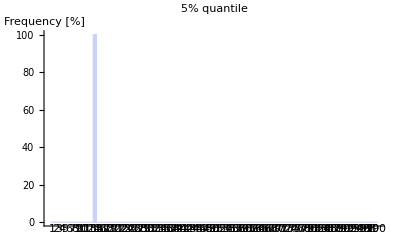
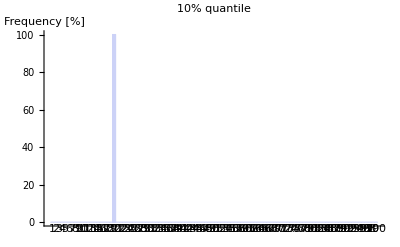
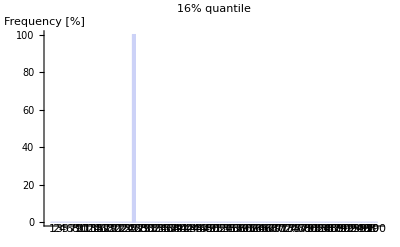
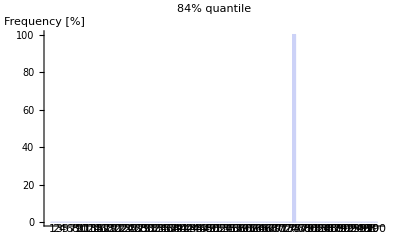
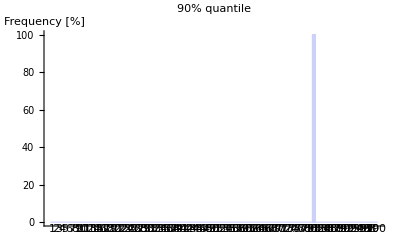
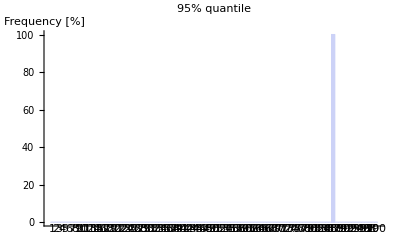

```mathematica
Table[ 
BarChart[histos[[j]]/Total[histos[[j]] ]*100,PlotLabel->ToString[ quantiles[[j]] ]<>"% quantile",AxesLabel-> "Frequency [%]" ,ChartLabels->Table[ToString[i],{i,nBins}]],
{j,Length[quantiles]}]
```

```mathematica
histos[[-1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,2,2,5,8,9,8,8,13,9,11,6,5,4,1,3,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total[ histos[[-1]] ]
```

100

mode, mean, std. dev. of the mode distribution

```mathematica
Position[ histos[[-1]] , Max[ histos[[-1]] ] ]
Total[histos[[-1]]*Range[nBins]]/nBins //N
Total[histos[[-1]]*(Range[nBins])^2 ]/nBins - %^2//Sqrt
```

{{51}}

50.68

3.77327